```mathematica
rhos={0.92333,1.2021,1.42239,1.50772,1.6,1.69997,1.80845,1.97531,2.42954,2.5155,2.8125}
```

{0.92333,1.2021,1.42239,1.50772,1.6,1.69997,1.80845,1.97531,2.42954,2.5155,2.8125}

```mathematica
files=Table[FileNames["S_T*_rho"<>ToString[rhos[[rho]]]<>".dat","/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/S/"],{rho,Length[rhos]}];
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0029_rho1.69997_kpeak.dat"]
```

```mathematica
fsfiles=Table[FileNames["Fs_T*_rho"<>ToString[rhos[[rho]]]<>"_kpeak.dat","/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/"],{rho,Length[rhos]}];
```

```mathematica
names =Table[FileNameTake/@files[[rho]],{rho,Length[rhos]}];
```

```mathematica
temperaturesVtrimer=Table[StringReplace[#,StartOfString~~"S_T"~~t__~~"_rho"<>ToString[rhos[[rho]]]<>".dat":>t]&/@names[[rho]],{rho,Length[rhos]}]
```

{{0.000175,0.0001,0.00025,0.00035,0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.007,0.008,0.009,0.015,0.01,0.03,0.05,0.06,0.07,0.08,0.09,0.15,0.1,0.5,0.65,1.5e-06,1e-05,1e-06,1e-07,1e-08,1e-09,2.5e-07,2.5e-08,2.5e-09,2e-05,2e-06,3.5e-06,4e-05,5e-05,5e-06,5e-07,5e-08,5e-09,6.5e-06,6e-07,7.5e-08,7.5e-09,7e-07,8e-06,8e-07},{0.000175,0.0001,0.00025,0.00035,0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.06,0.07,0.09,0.15,0.1,1.25e-06,1e-05,1e-06,1e-07,1e-08,2.5e-07,2.5e-08,2e-05,2e-06,3e-05,4e-05,5e-05,5e-06,5e-07,5e-08,6e-07,7.5e-08,8e-06,8e-07},{0.0001,0.00025,0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.05,0.07,0.08,0.09,0.15,0.1,1e-05,1e-06,1e-07,1e-08,2.5e-07,2.5e-08,2e-06,5e-05,5e-06,5e-07,5e-08,7.5e-07,7.5e-08,8e-06},{0.0001,0.00025,0.0005,0.00075,0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.005,0.007,0.008,0.015,0.01,0.03,0.05,0.06,0.07,0.08,0.09,0.15,0.1,1e-05,1e-06,2.5e-05,2.5e-06,5e-05,5e-06,6e-06,7.5e-06},{0.00015,0.0001,0.0003,0.0009,0.0013,0.001,0.0022,0.002,0.0033,0.0035,0.0045,0.004,0.0055,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.05,0.06,0.07,0.08,0.09,0.15,0.1,1e-05,2e-05,3e-05,5e-05,5e-06,7e-05},{0.00095,0.00105,0.0011,0.0012,0.0013,0.0014,0.0015,0.0017,0.0018,0.001,0.0022,0.0025,0.0027,0.0028,0.0029,0.002,0.0031,0.0032,0.0033,0.0034,0.0036,0.0037,0.0038,0.003,0.004,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.06,0.07,0.08,0.09,0.15,0.1},{0.001,0.0025,0.002,0.0035,0.003,0.00505,0.0051,0.00535,0.0055,0.00575,0.0059,0.005,0.0061,0.0063,0.0065,0.00725,0.0075,0.00775,0.007,0.00825,0.0085,0.008,0.009,0.015,0.01,0.03,0.05,0.06,0.07,0.08,0.09,0.15,0.1,0.3},{0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.005,0.007,0.008,0.009,0.015,0.01,0.032,0.033,0.035,0.03,0.044,0.045,0.04,0.05,0.06,0.07,0.08,0.09,0.15},{0.001,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.04,0.05,0.061,0.062,0.063,0.064,0.065,0.0685,0.068,0.0695,0.069,0.06,0.07,0.08,0.09,0.15,0.1,0.3},{0.035,0.045,0.04,0.0515,0.051,0.0525,0.052,0.053,0.054,0.055,0.05,0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.06,0.07,0.08,0.09,0.15,0.1},{0.001,0.007,0.008,0.009,0.015,0.01,0.03,0.05,0.061,0.0625,0.065,0.06,0.07,0.08,0.09,0.15,0.1,0.3}}

```mathematica
temperaturesVtrimer=Table[ToExpression@StringReplace[temperaturesVtrimer[[rho]],("e")->"*^"],{rho,Length[rhos]}]
```

{{0.000175,0.0001,0.00025,0.00035,0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.007,0.008,0.009,0.015,0.01,0.03,0.05,0.06,0.07,0.08,0.09,0.15,0.1,0.5,0.65,1.5×10^-6,1/100000,1/1000000,1/10000000,1/100000000,1/1000000000,2.5×10^-7,2.5×10^-8,2.5×10^-9,1/50000,1/500000,3.5×10^-6,1/25000,1/20000,1/200000,1/2000000,1/20000000,1/200000000,6.5×10^-6,3/5000000,7.5×10^-8,7.5×10^-9,7/10000000,1/125000,1/1250000},{0.000175,0.0001,0.00025,0.00035,0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.06,0.07,0.09,0.15,0.1,1.25×10^-6,1/100000,1/1000000,1/10000000,1/100000000,2.5×10^-7,2.5×10^-8,1/50000,1/500000,3/100000,1/25000,1/20000,1/200000,1/2000000,1/20000000,3/5000000,7.5×10^-8,1/125000,1/1250000},{0.0001,0.00025,0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.05,0.07,0.08,0.09,0.15,0.1,1/100000,1/1000000,1/10000000,1/100000000,2.5×10^-7,2.5×10^-8,1/500000,1/20000,1/200000,1/2000000,1/20000000,7.5×10^-7,7.5×10^-8,1/125000},{0.0001,0.00025,0.0005,0.00075,0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.005,0.007,0.008,0.015,0.01,0.03,0.05,0.06,0.07,0.08,0.09,0.15,0.1,1/100000,1/1000000,0.000025,2.5×10^-6,1/20000,1/200000,3/500000,7.5×10^-6},{0.00015,0.0001,0.0003,0.0009,0.0013,0.001,0.0022,0.002,0.0033,0.0035,0.0045,0.004,0.0055,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.05,0.06,0.07,0.08,0.09,0.15,0.1,1/100000,1/50000,3/100000,1/20000,1/200000,7/100000},{0.00095,0.00105,0.0011,0.0012,0.0013,0.0014,0.0015,0.0017,0.0018,0.001,0.0022,0.0025,0.0027,0.0028,0.0029,0.002,0.0031,0.0032,0.0033,0.0034,0.0036,0.0037,0.0038,0.003,0.004,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.06,0.07,0.08,0.09,0.15,0.1},{0.001,0.0025,0.002,0.0035,0.003,0.00505,0.0051,0.00535,0.0055,0.00575,0.0059,0.005,0.0061,0.0063,0.0065,0.00725,0.0075,0.00775,0.007,0.00825,0.0085,0.008,0.009,0.015,0.01,0.03,0.05,0.06,0.07,0.08,0.09,0.15,0.1,0.3},{0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.005,0.007,0.008,0.009,0.015,0.01,0.032,0.033,0.035,0.03,0.044,0.045,0.04,0.05,0.06,0.07,0.08,0.09,0.15},{0.001,0.005,0.007,0.008,0.009,0.015,0.01,0.03,0.04,0.05,0.061,0.062,0.063,0.064,0.065,0.0685,0.068,0.0695,0.069,0.06,0.07,0.08,0.09,0.15,0.1,0.3},{0.035,0.045,0.04,0.0515,0.051,0.0525,0.052,0.053,0.054,0.055,0.05,0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.06,0.07,0.08,0.09,0.15,0.1},{0.001,0.007,0.008,0.009,0.015,0.01,0.03,0.05,0.061,0.0625,0.065,0.06,0.07,0.08,0.09,0.15,0.1,0.3}}

```mathematica
idx=Table[Reverse[Ordering[temperaturesVtrimer[[rho]]]],{rho,Length[rhos]}]
```

{{26,25,23,24,22,21,20,19,18,17,15,16,14,13,12,11,9,10,7,6,8,5,4,3,1,2,40,39,36,28,50,45,41,38,37,27,29,51,49,46,42,33,30,47,43,34,31,48,44,35,32},{22,23,21,20,19,18,16,17,15,14,13,12,11,9,10,7,6,8,5,4,3,1,2,35,34,33,31,25,41,36,32,24,26,42,39,37,29,27,40,38,30,28},{21,22,20,19,18,17,16,14,15,13,12,11,10,9,7,8,5,4,6,3,2,1,30,23,36,31,29,24,34,32,27,25,35,33,28,26},{23,24,22,21,20,19,18,17,15,16,14,13,12,11,9,10,7,6,8,5,4,3,2,1,29,27,25,32,31,30,28,26},{26,27,25,24,23,22,21,20,18,19,17,16,15,13,14,11,12,10,9,7,8,5,6,4,3,1,2,33,31,30,29,28,32},{37,38,36,35,34,33,32,30,31,29,28,27,26,25,23,22,21,20,19,18,17,24,15,14,13,12,11,16,9,8,7,6,5,4,3,2,10,1},{34,32,33,31,30,29,28,27,26,24,25,23,21,20,22,18,17,16,19,15,14,13,11,10,9,8,7,6,12,4,5,2,3,1},{26,25,24,23,22,21,19,18,20,16,15,14,17,12,13,11,10,9,8,7,5,6,3,2,4,1},{26,24,25,23,22,21,18,19,16,17,15,14,13,12,11,20,10,9,8,6,7,5,4,3,2,1},{25,26,24,23,22,20,19,18,17,16,15,14,13,12,21,10,9,8,6,7,4,5,11,2,3,1},{18,16,17,15,14,13,11,10,9,12,8,7,5,6,4,3,2,1}}

```mathematica
sortedTemperaturesVitrimer=Table[temperaturesVtrimer[[rho,idx[[rho]]]],{rho,Length[rhos]}]
```

{{0.65,0.5,0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,1/50000,1/100000,1/125000,6.5×10^-6,1/200000,3.5×10^-6,1/500000,1.5×10^-6,1/1000000,1/1250000,7/10000000,3/5000000,1/2000000,2.5×10^-7,1/10000000,7.5×10^-8,1/20000000,2.5×10^-8,1/100000000,7.5×10^-9,1/200000000,2.5×10^-9,1/1000000000},{0.15,0.1,0.09,0.07,0.06,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,3/100000,1/50000,1/100000,1/125000,1/200000,1/500000,1.25×10^-6,1/1000000,1/1250000,3/5000000,1/2000000,2.5×10^-7,1/10000000,7.5×10^-8,1/20000000,2.5×10^-8,1/100000000},{0.15,0.1,0.09,0.08,0.07,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00025,0.0001,1/20000,1/100000,1/125000,1/200000,1/500000,1/1000000,7.5×10^-7,1/2000000,2.5×10^-7,1/10000000,7.5×10^-8,1/20000000,2.5×10^-8,1/100000000},{0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00075,0.0005,0.00025,0.0001,1/20000,0.000025,1/100000,7.5×10^-6,3/500000,1/200000,2.5×10^-6,1/1000000},{0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.0055,0.005,0.0045,0.004,0.0035,0.0033,0.0022,0.002,0.0013,0.001,0.0009,0.0003,0.00015,0.0001,7/100000,1/20000,3/100000,1/50000,1/100000,1/200000},{0.15,0.1,0.09,0.08,0.07,0.06,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0038,0.0037,0.0036,0.0034,0.0033,0.0032,0.0031,0.003,0.0029,0.0028,0.0027,0.0025,0.0022,0.002,0.0018,0.0017,0.0015,0.0014,0.0013,0.0012,0.0011,0.00105,0.001,0.00095},{0.3,0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.0085,0.00825,0.008,0.00775,0.0075,0.00725,0.007,0.0065,0.0063,0.0061,0.0059,0.00575,0.0055,0.00535,0.0051,0.00505,0.005,0.0035,0.003,0.0025,0.002,0.001},{0.15,0.09,0.08,0.07,0.06,0.05,0.045,0.044,0.04,0.035,0.033,0.032,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001},{0.3,0.15,0.1,0.09,0.08,0.07,0.0695,0.069,0.0685,0.068,0.065,0.064,0.063,0.062,0.061,0.06,0.05,0.04,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.001},{0.15,0.1,0.09,0.08,0.07,0.069,0.068,0.067,0.066,0.065,0.064,0.063,0.062,0.061,0.06,0.055,0.054,0.053,0.0525,0.052,0.0515,0.051,0.05,0.045,0.04,0.035},{0.3,0.15,0.1,0.09,0.08,0.07,0.065,0.0625,0.061,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.001}}

```mathematica
sortedFilenamesVitrimer=Table[files[[rho]][[idx[[rho]]]],{rho,Length[rhos]}];
```

```mathematica
sortedFsFilenamesVitrimer=Table[fsfiles[[rho]][[idx[[rho]]]],{rho,Length[rhos]}];
```

```mathematica
SkVitrimer=Table[Import[#,"Data"]&/@sortedFilenamesVitrimer[[rho]],{rho,Length[rhos]}];
```

```mathematica
fsVitrimer=Table[Import[#,"Data"]&/@sortedFsFilenamesVitrimer[[rho]],{rho,Length[rhos]}];
```

```mathematica
SkVitrimer[[1,1]]
```

{{0.20944,0.467318,1},{0.31416,0.461731,1},{0.41888,0.476014,1},{0.5236,0.456288,1},{0.62832,0.468596,1},{0.73304,0.47525,1},{0.83776,0.490466,1},{0.94248,0.503919,1},{1.0472,0.497835,1},{1.15192,0.498399,1},{1.25664,0.516119,1},{1.36136,0.517873,1},{1.46608,0.535053,1},{1.5708,0.539776,1},{1.67552,0.55229,1},{1.78024,0.553095,1},{1.88496,0.549565,1},{1.98968,0.529856,1},{2.0944,0.517871,1},{2.19912,0.495184,1},{2.30384,0.477428,1},{2.40856,0.461807,1},{2.51328,0.456237,1},{2.618,0.438922,1},{2.72272,0.437171,1},{2.82744,0.432457,1},{2.93216,0.430189,1},{3.03688,0.438582,1},{3.1416,0.437794,1},{3.24632,0.438501,1},{3.35104,0.444629,1},{3.45576,0.454989,1},{3.56048,0.451296,1},{3.6652,0.467028,1},{3.76992,0.46898,1},{3.87464,0.47959,1},{3.97936,0.486223,1},{4.08408,0.493155,1},{4.1888,0.505899,1},{4.29352,0.523711,1},{4.39824,0.540364,1},{4.50296,0.552543,1},{4.60768,0.576282,1},{4.7124,0.579763,1},{4.81712,0.609886,1},{4.92184,0.62758,1},{5.02656,0.645003,1},{5.13128,0.668659,1},{5.236,0.688449,1},{5.34072,0.723074,1},{5.44544,0.743135,1},{5.55016,0.763213,1},{5.65488,0.79629,1},{5.7596,0.836774,1},{5.86432,0.847187,1},{5.96904,0.871131,1},{6.07376,0.892031,1},{6.17848,0.922652,1},{6.2832,0.95277,1},{6.38792,0.969014,1},{6.49264,0.988558,1},{6.59736,1.00116,1},{6.70208,1.02984,1},{6.8068,1.05071,1},{6.91152,1.05977,1},{7.01624,1.07075,1},{7.12096,1.08851,1},{7.22568,1.08086,1},{7.3304,1.09333,1},{7.43512,1.10582,1},{7.53984,1.11908,1},{7.64456,1.10758,1},{7.74928,1.13303,1},{7.854,1.11819,1},{7.95872,1.11573,1},{8.06344,1.12197,1},{8.16816,1.11217,1},{8.27288,1.12272,1},{8.3776,1.10131,1},{8.48232,1.1116,1},{8.58704,1.10142,1},{8.69176,1.09307,1},{8.79648,1.0942,1},{8.9012,1.08903,1},{9.00592,1.08429,1},{9.11064,1.08017,1},{9.21536,1.06522,1},{9.32008,1.07288,1},{9.4248,1.06381,1},{9.52952,1.04751,1},{9.63424,1.04872,1},{9.73896,1.03744,1},{9.84368,1.03095,1},{9.9484,1.04681,1},{10.0531,1.0266,1},{10.1578,1.03186,1},{10.2626,1.00989,1},{10.3673,1.00831,1},{10.472,1.01071,1},{10.5767,0.999969,1},{10.6814,0.989921,1},{10.7862,0.996759,1},{10.8909,0.996533,1},{10.9956,0.992432,1},{11.1003,0.988826,1},{11.205,0.996311,1},{11.3098,0.978744,1},{11.4145,0.985159,1},{11.5192,0.97325,1},{11.6239,0.981812,1},{11.7286,0.967977,1},{11.8334,0.972642,1},{11.9381,0.963117,1},{12.0428,0.964835,1},{12.1475,0.975029,1},{12.2522,0.975012,1},{12.357,0.960057,1},{12.4617,0.975679,1},{12.5664,0.963295,1},{12.6711,0.952941,1},{12.7758,0.961266,1},{12.8806,0.966717,1},{12.9853,0.96156,1},{13.09,0.969294,1},{13.1947,0.965533,1},{13.2994,0.973801,1},{13.4042,0.975934,1},{13.5089,0.986825,1},{13.6136,0.962128,1},{13.7183,0.970934,1},{13.823,0.978396,1},{13.9278,0.974601,1},{14.0325,0.987213,1},{14.1372,0.989801,1},{14.2419,0.986778,1},{14.3466,0.994688,1},{14.4514,0.988242,1},{14.5561,0.994731,1},{14.6608,0.994196,1},{14.7655,0.995145,1},{14.8702,0.998178,1},{14.975,0.993529,1},{15.0797,0.999381,1},{15.1844,1.00588,1},{15.2891,1.00101,1},{15.3938,1.01489,1},{15.4986,1.00701,1},{15.6033,1.00828,1},{15.708,1.01304,1},{15.8127,1.00855,1},{15.9174,1.01656,1},{16.0222,1.01449,1},{16.1269,1.01058,1},{16.2316,1.02696,1},{16.3363,1.01315,1},{16.441,1.01904,1},{16.5458,1.02452,1},{16.6505,1.01183,1},{16.7552,1.02163,1},{16.8599,1.01736,1},{16.9646,1.01001,1},{17.0694,1.01603,1},{17.1741,1.01934,1},{17.2788,1.00073,1},{17.3835,1.01796,1},{17.4882,1.00872,1},{17.593,1.01414,1},{17.6977,1.00742,1},{17.8024,1.00725,1},{17.9071,1.02617,1},{18.0118,1.0077,1},{18.1166,1.00423,1},{18.2213,0.99811,1},{18.326,1.01878,1},{18.4307,1.01175,1},{18.5354,0.999972,1},{18.6402,1.00747,1},{18.7449,0.995513,1},{18.8496,1.01695,1},{18.9543,1.02154,1},{19.059,1.0057,1},{19.1638,1.00714,1},{19.2685,1.01243,1},{19.3732,1.0067,1},{19.4779,1.00351,1},{19.5826,1.0094,1},{19.6874,1.01026,1},{19.7921,1.00995,1},{19.8968,0.997265,1},{20.0015,0.99738,1},{20.1062,1.00204,1},{20.211,1.01148,1},{20.3157,0.97542,1},{20.4204,0.984114,1},{20.5251,0.994422,1},{20.6298,0.994263,1},{20.7346,0.986091,1},{20.8393,0.994828,1},{20.944,0.995133,1},{21.0487,0.991383,1},{21.1534,0.985239,1},{21.2582,0.997164,1},{21.3629,0.985122,1},{21.4676,0.991049,1},{21.5723,0.992569,1},{21.677,0.998236,1},{21.7818,0.987081,1},{21.8865,0.983123,1},{21.9912,0.984852,1},{22.0959,0.985138,1},{22.2006,0.988948,1},{22.3054,0.988861,1},{22.4101,0.991889,1},{22.5148,0.988167,1},{22.6195,0.994521,1},{22.7242,1.00672,1},{22.829,0.985525,1},{22.9337,0.978037,1},{23.0384,0.99485,1},{23.1431,0.994264,1},{23.2478,0.998511,1},{23.3526,0.992431,1},{23.4573,1.00899,1},{23.562,0.996084,1},{23.6667,0.995917,1},{23.7714,0.989999,1}}

```mathematica
skmax=Table[Table[Max[SkVitrimer[[rho,T,;;,2]]],{T,Length[SkVitrimer[[rho]]]}],{rho,Length[rhos]}]
```

{{1.13303,1.14905,1.29543,1.34016,1.34317,1.36009,1.37969,1.38499,1.40641,1.43319,1.46383,1.48053,1.4782,1.48402,1.48239,1.48859,1.49074,1.49334,1.49247,1.49657,1.49879,1.49994,1.49972,1.51192,1.50694,1.51632,1.51536,1.50466,1.52627,1.5036,1.51136,1.50981,1.50265,1.49417,1.48903,1.49131,1.46957,1.45979,1.45696,1.47898,1.45406,1.43356,1.47345,1.45094,1.50282,1.50352,1.5261,1.58665,1.53432,1.55908,1.54614},{1.37711,1.46026,1.46968,1.50706,1.53332,1.62624,1.69197,1.73112,1.74313,1.75068,1.76324,1.78229,1.79159,1.79377,1.79376,1.81864,1.80505,1.81781,1.82727,1.84038,1.85613,1.84774,1.85829,1.87383,1.86592,1.87101,1.87562,1.88431,1.87934,1.89024,1.95618,1.97279,2.00858,2.05635,2.15242,2.15989,2.23135,2.31188,2.26444,2.30359,2.25649,2.24468},{1.484,1.58889,1.60638,1.65147,1.65991,1.75912,1.87536,2.02279,2.10683,2.1398,2.15352,2.17944,2.21949,2.25358,2.25938,2.27173,2.29522,2.29077,2.31795,2.34758,2.39675,2.42936,2.44122,2.55549,2.54103,2.62018,2.74958,2.97657,3.14284,3.14855,3.1554,3.14135,3.09696,3.08262,3.15227,3.15078},{1.5214,1.64108,1.67768,1.70982,1.74162,1.80236,1.85169,2.0034,2.19148,2.30507,2.3675,2.37234,2.45751,2.49243,2.5146,2.54797,2.5649,2.58357,2.58504,2.65065,2.65973,2.69074,2.70186,2.75178,2.75054,2.85387,2.95562,2.96758,2.96208,2.96744,3.15104,3.25081},{1.57458,1.71847,1.7459,1.78991,1.83682,1.88952,1.96195,2.15174,2.41652,2.56799,2.6012,2.6389,2.67962,2.75131,2.77584,2.80895,2.82347,2.84758,2.86607,2.932,2.93337,2.9983,3.02844,3.06225,3.10301,3.14377,3.23615,3.25394,3.28563,3.34442,3.25208,3.33014,3.45395},{1.63205,1.79974,1.83973,1.87986,1.94598,2.01607,2.34667,2.69434,2.88843,2.92834,2.98032,3.03743,3.1793,3.22318,3.22773,3.2924,3.24723,3.36727,3.25659,3.33571,3.32686,3.31215,3.29893,3.49168,3.2817,3.32222,3.45504,3.24575,3.56334,3.28377,3.39332,3.57942,3.5297,3.41815,3.5664,3.65003,3.26989,3.4742},{1.44509,1.70264,1.8937,1.95072,2.01037,2.08076,2.165,2.26544,2.57597,3.02313,3.30928,3.30515,3.38663,3.47276,3.47516,3.52978,3.38023,3.47313,3.46279,3.42253,3.37608,3.4071,3.62323,3.59863,3.57007,3.62078,3.64977,3.62067,3.45404,3.60025,3.56931,3.76009,3.36955,3.58588},{1.98046,2.38121,2.49557,2.64186,2.77036,2.97539,3.09309,3.1223,3.21793,3.39807,3.47254,3.57886,3.43143,3.57457,3.69756,3.69792,3.72127,3.7008,3.61887,3.82037,3.71416,3.71453,3.71168,3.81054,3.71371,3.67014},{1.78069,2.33149,2.87114,3.03224,3.21857,3.4225,3.40312,3.49764,3.44029,3.50019,3.57949,3.61859,3.67347,3.52616,3.64579,3.767,3.7636,3.88385,3.8511,3.93405,3.95947,3.97199,3.96718,3.99323,3.99568,3.99687},{2.21928,2.68348,2.80648,2.95725,3.14437,3.14532,3.17469,3.2032,3.24499,3.24389,3.26191,3.31034,3.30476,3.33288,3.36891,3.44424,3.45122,3.56933,3.58103,3.59226,3.54236,3.52277,3.62344,3.81307,3.90008,3.93482},{1.88356,2.34311,2.88789,3.04314,3.2712,3.47022,3.71343,3.53999,3.58127,3.62965,3.56153,3.70821,3.81366,4.26544,3.84825,4.26165,3.8429,3.89126}}

```mathematica
tauAlpha=Table[Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho"<>ToString[rhos[[r]]]<>".csv","Data"][[;;,1]],{r,Length[rhos]}]
```

{{0.0325164,0.0387735,0.0811996,0.109519,0.117507,0.130594,0.142607,0.155724,0.170049,0.225355,0.3438,0.424644,0.439858,0.471938,0.51535,0.682959,0.745781,0.786215,0.889292,0.954153,1.06042,1.53457,2.64807,2.943,3.57163,4.90282,6.97127,7.88525,12.0297,18.0323,19.0099,21.1271,25.64,29.5164,45.8296,56.6065,84.8521,102.977,141.357,180.853,275.908,1051.13,5033.97,7816.16},{0.0829651,0.115909,0.135802,0.153607,0.173746,0.269771,0.418869,0.545416,0.595586,0.627876,0.685631,0.846857,0.992169,1.06453,1.24724,1.36196,1.4613,1.54052,2.35021,4.05568,4.92198,5.56727,7.50894,11.2557,12.9575,16.5773,18.7512,31.2382,37.2493,53.9048,146.993,307.832,521.913,1000.92,3142.16,5143.29},{0.0918454,0.135273,0.147716,0.158489,0.173068,0.229356,0.3438,0.647836,0.921152,1.00588,1.15796,1.30978,1.73576,2.03367,2.30029,2.55649,2.943,3.27077,3.50932,5.74428,14.5993,26.0952,41.9691,171.552,235.491,467.804,3865.99},{0.0902431,0.140119,0.150338,0.164167,0.182451,0.199234,0.237573,0.388874,0.745781,1.30978,1.6465,1.79795,2.69509,3.4481,3.69958,4.65067,5.64407,6.27267,6.97127,13.3695,16.8065,23.0705,39.8107,83.3718,149.021,317.622,1051.13,1720.56,2917.21,4691.78},{0.0947646,0.142051,0.155117,0.172393,0.18825,0.224476,0.282184,0.445922,1.23758,2.1735,2.59175,3.09048,3.88498,5.42765,5.92692,8.42743,10.4092,13.0851,14.5425,29.4026,33.848,68.4331,106.251,118.085,390.788,1597.38,3404.64,5286.33,7385.46},{0.106221,0.162051,0.176957,0.196665,0.226399,0.269965,0.662393,2.43624,7.00381,9.78492,14.6674,23.1782,93.0896,313.527,430.397,495.468,782.938,870.166,1037.61,1259.25,1555.36,1955.21,2414.98,2637.12,4882.38},{0.0561106,0.107609,0.173068,0.192343,0.21756,0.259426,0.320429,0.417236,1.11791,12.2433,211.892,688.996,1548.14,3242.11,3299.68,8840.91},{0.155724,0.356117,0.533812,0.828841,1.56182,4.48982,10.4498,13.1362,39.1162,399.277,1442.9,4004.5},{0.0708098,0.218406,1.00976,2.19048,7.24911,66.5775,86.6916,94.6691,125.459,157.712,600.816,656.082,1326.49,2729.49,4020.07,4878.77},{0.184966,0.590952,0.96731,2.02575,6.94414,8.13596,9.04209,10.4092,11.5685,17.6488,22.9808,28.8887,38.2844,51.6367,70.8824,555.677,1047.09,2116.9,2436.96,3717.81,4355.9,6529.41},{0.0811996,0.298648,2.42501,7.47972,50.9338,3603.2}}

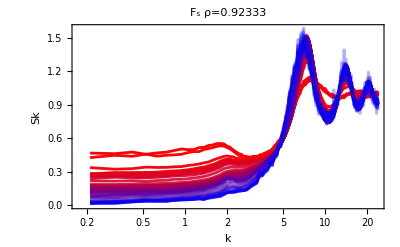
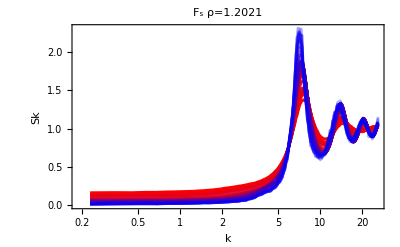
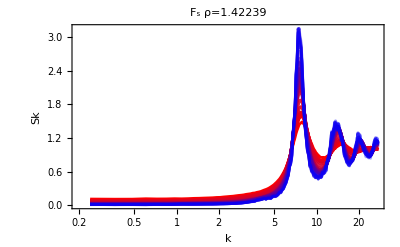
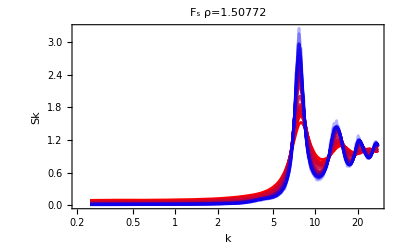
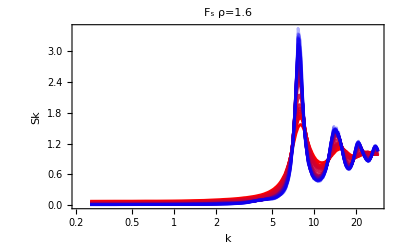
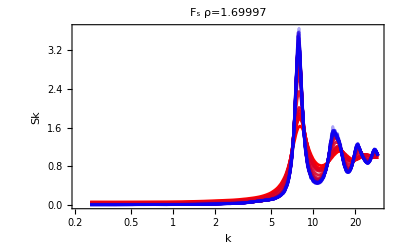
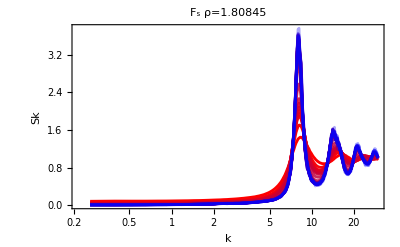
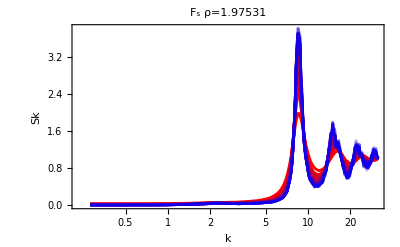

```mathematica
skvitrimerPlot=Table[Show[ListLogLinearPlot[Table[SkVitrimer[[rho,T,;;,1;;2]],{T,Length[SkVitrimer[[rho]]]}],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[SkVitrimer[[rho]]]],Joined->True,PlotLabel->"F_s ρ="<>ToString[rhos[[rho]]],FrameLabel->{"k","Sk"}]],{rho,Length[rhos]}]
```

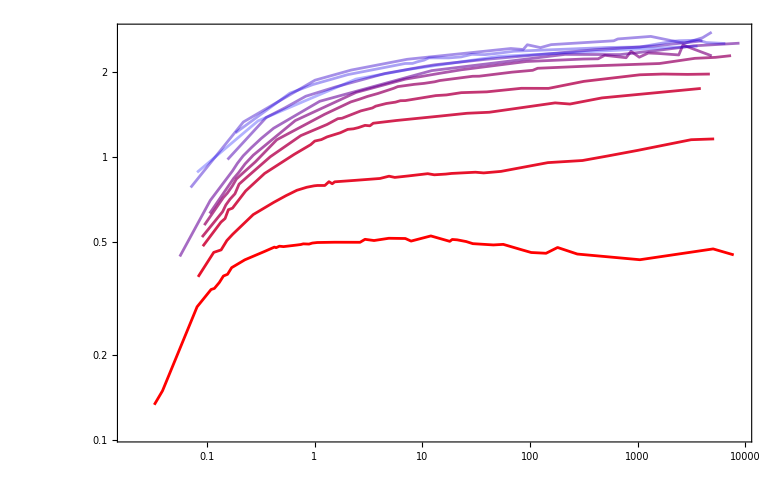

```mathematica
ListLogLogPlot[Table[Table[{tauAlpha[[p,T]],skmax[[p,T]]-1},{T,Length[tauAlpha[[p]]]}],{p,Length[rhos]}],PlotStyle->redBluePlotConfig[Length[rhos]],Joined->True]
```

```mathematica
sortedTemperaturesVitrimer[[1,{4,12,22,26}]]
```

{0.1,0.01,0.001,0.0001}

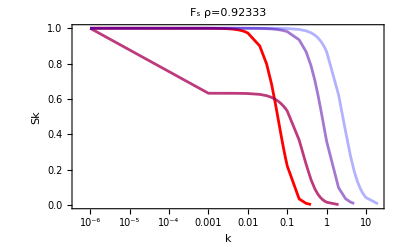

```mathematica
Table[Show[ListLogLinearPlot[fsVitrimer[[rho,{4,12,22,26},;;,1;;2]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[4],Joined->True,PlotLabel->"F_s ρ="<>ToString[rhos[[rho]]],FrameLabel->{"k","Sk"}]],{rho,1}]
```